# Assignment 6 - 2/27/14

## Cameron Embree, Group: Allie

Challenge 1: Describe how you can use linear least squares to fit power functions of the form f(x)= a^x or g(x)=x^a using the log function.  Following the class example of recovering a noisey sign curve, construct some noisey power functions, and try to recover the “a” using linear least squares.

```mathematica
(*Challenge 1 solution by:*)
```

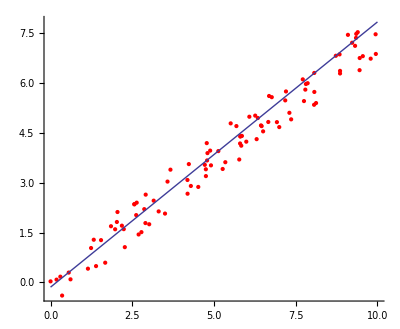

```mathematica
ClearAll["Global`*"]

a=.75;
b=1.112;
line[x_]:=a*x
xdat=RandomReal[{0,10},100];
ydat=(line /@ xdat)+RandomReal[{-.7,.7},100];
Graphics[Point[Transpose[{xdat,ydat}]], Axes->True];

aa=Transpose[{ConstantArray[1,100],xdat,#^2&/@xdat}];
approx=LeastSquares[aa,ydat];

Show[Graphics[{Red,Point[Transpose[{xdat,ydat}]]}, Axes->True],Plot[approx[[1]]+approx[[2]]x,{x,0,10}]]
```

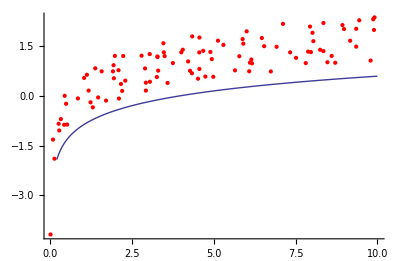

```mathematica
ClearAll["Global`*"]

a=.75;
b=1.112;
line[x_]:=a*Log[x]
xdat=RandomReal[{0,10},100];
ydat=(line /@ xdat)+RandomReal[{-.7,.7},100];
Graphics[Point[Transpose[{xdat,ydat}]], Axes->True];

aa=Transpose[{ConstantArray[1,100],xdat,#^2&/@xdat}];
approx=LeastSquares[aa,ydat];

Show[Graphics[{Red,Point[Transpose[{xdat,ydat}]]}, Axes->True],Plot[approx[[1]]+approx[[2]]*Log[x],{x,0,10}]]
```

Challenge 2:  Find the constant function that best fits the following x,y pairs: {{-1,5/4},{2,4/3},{3,5/12}}.  Plot the points with the best fit constant function.

```mathematica
(*Challenge 2 solution by:*)
```

{{-1,5/4},{2,4/3},{3,5/12}}

1.20513-0.153846 x

1.75+0.263889 x-0.236111 x^2

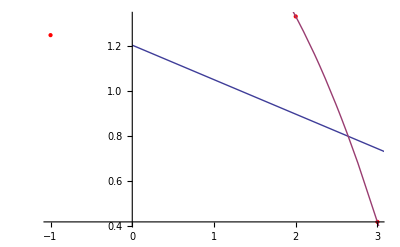

```mathematica
dat={{-1,5/4},{2,4/3},{3,5/12}}
line = Fit[dat, {1,x},x]
parabola = Fit[dat, {1,x,x^2}, x]

Show[ListPlot[dat, PlotStyle->Red], Plot[{line, parabola}, {x, 0, 100}]]

Graphics[List[Point[{-1,5/4}],Point[{2,4/3}],Point[{3,5/12}]],Axes->True];
```

Challenge 3: Find the parabola of the form ax^2+b that best fits the following x,y points {{-13.1},{0,.9},{1,2.9}}.  Plot the points and the best fit parabola.

```mathematica
(*Challenge 3 solution by:*)
```

5.97341-0.0290843 x^2

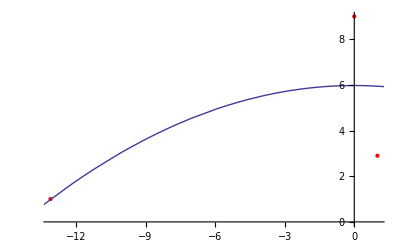

```mathematica
dat={{-13.1,1},{0,9},{1,2.9}};
parabola = Fit[dat, {1,x^2}, x]

Show[ListPlot[dat, PlotStyle->Red], Plot[ parabola,{x,-100,100}]]
```

Challenge 4:  Find the first, second, third, fourth and fifth degree polynomial fits to the following data and plot the data and polynomials. {{0,.7829},{.1,.8052},{.2,.5753},{.3,5201},{.4,.3783},{.5,.2923},{.6,1695},{.7,.0842},{.8,.0415},{.9,.009},{0,1}}

```mathematica
(*Challenge 4 solution by:*)
```

726.522-242.616 x

23.2063+6470.85 x-7885.66 x^2

-271.006+14418. x-32721.8 x^2+18892.4 x^3

-187.892+8630.04 x+1613.02 x^2-43588.3 x^3+35088.2 x^4

-33.9296-19853.2 x+275085. x^2-913201. x^3+1.14943×10^6 x^4-497058. x^5

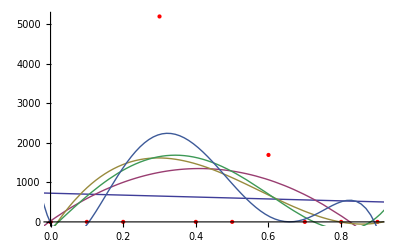

```mathematica
dat={{0,.7829},{.1,.8052},{.2,.5753},{.3,5201},{.4,.3783},{.5,.2923},{.6,1695},{.7,.0842},{.8,.0415},{.9,.009},{0,1}};

One = Fit[dat, {1,x}, x]
Two=Fit[dat,{1,x,x^2},x]
Three=Fit[dat,{1,x,x^2,x^3},x]
Four=Fit[dat,{1,x,x^2,x^3,x^4},x]
Five=Fit[dat,{1,x,x^2,x^3,x^4,x^5},x]

Show[ListPlot[dat, PlotStyle->Red], Plot[{One, Two,Three,Four,Five}, {x, -20, 20}]]
```

Challenge 5:  Find the best fitting function of the form y[x_]:=a Exp[bx]/(1+x)^c to the data {{0,1.996},{.4,1.244},{.3,.810},{.8,.541},{1.0,.259}}.  Hint: you may want to take the log of the function y.

```mathematica
(*Challenge 5 solution by:*)
```

```mathematica
dat={{0,1.996},{.4,1.244},{.3,.810},{.8,.541},{1.0,.259}};

(* FUNCTION: y[x_]:=a* Exp[b*x]/(1+x)^c *)
```

Challenge 6: The f(x) be the piecewise function on the interval [-1,1] where if x  >= 0 the f(x)=1 and if x<0, f(x)=1.  Find the constants a and b using linear least squares to approximate f by the function g(x)=a Cos[Pi x]+ b Sin [Pi x].  You’ll need the choose the amount of data points and which data points yourself.  How does the approximate function g(x) change as the number of the data points you use increase?

```mathematica
(*Challenge 6 solution by:*)
```

Challenge 7: Health vs. Weath is a commonly used way to judge how “developed” nations are.  Using CountryData, extract as ordered pairs Life Expectancy and GPD (in us dollars) for each country on earth and plot these points. Find the best fit line for this data.  Which countries are the most developed using the health v wealth measure, which ones are the least developed

```mathematica
(*Challenge 7 solution by:*)
```

-1.96143×10^8+1.90929×10^7 x-767993. x^2+16339.9 x^3-193.944 x^4+1.21762 x^5-0.00315882 x^6

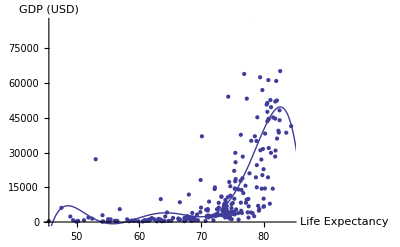

```mathematica
a=CountryData["Countries", "LifeExpectancy"];
b=CountryData["Countries", "GDPPerCapita"];

dat=Partition[Riffle[a,b],2];

trimmedDat=DeleteCases[dat,{___,_Missing|_Missing,___}];
fitLine=Fit[trimmedDat,{1,x,x^2,x^3,x^4,x^5,x^6},x]

getColor[x1_,y1_]:=Module[{},
(*Print[" X: ",x1," Y: ",y1, " FUNC: ",fitLine, " ESTIMATED: ",val];*)
val=fitLine/.x->x1;
If[val>y1,Red,Blue]
]

Show[ListPlot[trimmedDat, 
AxesLabel->{"Life Expectancy","GDP (USD)"},
ColorFunctionScaling->False,
ColorFunction->Function[{x1,y1},If[(fitLine/.x->x1)>y1,Red,Blue]]
], 
Plot[{fitLine}, {x, 0, 100}]
]
```

Challenge 9:We can make a simpler version of the team ranking system by just noting which team won,with a+1 or-1 instead of the score difference.How deos this affect the power rankings you did for assignment 5?(for more variations on this theme check out the team ranking pdf I put up on blackboard)

```mathematica
(*Challenge 8 solution by:*)
```